## Basic Concepts and Built-In Functions

## Learning Objectives

Become familiar with common terms and definitions associated with machine learning

Use Wolfram Language functions for machine learning tasks

Know about different machine learning paradigms

## Definitions

### What Is Machine Learning?

Machine learning is the process where a computer “learns” a model from data. Instead of giving explicit instructions to the computer to do something, you program it to do some tasks by showing it examples.

#### Useful terms

Data: Digital information collected for the task

Dataset: A set of data examples (or observations or samples) to learn from

Independent variables (or predictor variables or features or attributes or input)

x⃗=={x_1 …,x_n}

Dependent variable (or response variables or label or output)

y

Model

A function and associated optimization criteria (e.g. distributional assumptions) used to approximate the behavior suggested by the data

y==f(x⃗)

A blackbox represented by an algorithm that takes training data as input and produces labels/predictions as output

x⃗→Blackbox→y

Learning

1) Process of identifying the function or the algorithm (and the corresponding parameters) that best represents the relationship between the input and output

2) Tuning parameters to fit data

(Parameters: Values in the model or algorithm that are not assumed by the predictor or response variables)

## Typical Tasks

Generate text:

“The cat sat on the …” → “mat”

Translate text:

“the house is blue” → “la maison est bleue”

Generate images:

“A friendly robot” → -Graphics-

## Typical Tasks

Classify images, sound, text, etc.

→cat, →dog,…

→cat, →dog,…
		"my cat is fast"→,"the big dog"→,…

Predict a variable in a dataset

(6 yo, female) → 1.15 m, (11 yo, male) → 1.48 m, …

Forecast future values in a time series

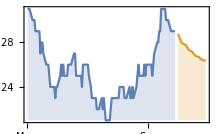

## Typical Tasks

Detect anomalies

-Graphics-

Cluster data

-Graphics-

A robot learning how to walk

## The “Traditional” Machine Learning Workflow

### Data

Get your hands on (preferably a lot of) data

### Model

Build a model or pick one from a repository of existing models

### Train

Train the model with your own data

### Test

Test the model to validate its performance

### Deploy

Provide the model for use by others

## Using Built-in Machine Learning in Wolfram Language

Wolfram Language has a number of built-in functions powered by machine learning that makes it possible for you to skip steps 1–4, so you can focus on step 5.

### Identify the Object in an Image

```mathematica
testImages = {-Graphics-,-Graphics-,-Graphics-,-Graphics-};
ImageIdentify[testImages]
```

### Generate an Image from Descriptive Text

This requires external service authentication, billing and internet connectivity. The following example was created with the OpenAI API:

```mathematica
ImageSynthesize["spaceship carrying people to mars",3]
```

{-Graphics-,-Graphics-,-Graphics-}

### Find the Facial Features in an Image

```mathematica
FacialFeatures[-Graphics-]//Dataset
```

### Recognize Handwritten Digits

```mathematica
Classify[,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

## Using Built-in Machine Learning in Wolfram Language

### Summarize Text

This requires access to a large language model (LLM) API:

```mathematica
TextSummarize[WikipediaData["SpaceX"]]
```

SpaceX, an American spacecraft manufacturer and launch service provider, was founded by Elon Musk in 2002 with the goal of reducing space transportation costs and colonizing Mars. The company operates the Falcon 9 and Falcon Heavy rockets, the Dragon and Starship spacecraft, and offers internet service via its Starlink satellites. SpaceX has achieved several milestones, including being the first private company to develop a liquid-propellant rocket that reached orbit and to send a spacecraft to the International Space Station. From 2019 to present, SpaceX has been involved in various projects, including the launch of the world's largest commercial satellite constellation, Starlink, and the development of the Starship launch vehicle. The company has also made history by launching two NASA astronauts into orbit. SpaceX operates manufacturing, refurbishment, development, and test facilities across the U.S., and has won numerous contracts from NASA and the U.S. military. The company's low launch prices have led to market pressure on competitors.

```mathematica
TextSummarize[WikipediaData["SpaceX"],"Keywords"]
```

{SpaceX,Elon Musk,space exploration,Falcon 9,Falcon Heavy,Dragon,Starship,Starlink satellites,Mars colonization,rocket launch.}

### Answer a Question Based on Text Provided

WikipediaData utilizes MediaWiki’s API to retrieve article and category contents and metadata from the English-language Wikipedia.

WikipediaSearch utilizes MediaWiki’s API to find article and category pages in the English-language Wikipedia:

```mathematica
question="Who was the architect of the Sagrada Familia?";
```

```mathematica
articles=WikipediaSearch["Content"->question]
```

```mathematica
contents=WikipediaData[articles];
```

```mathematica
FindTextualAnswer[contents,question]
```

### Classify Sentiment

```mathematica
Classify["Sentiment",{"I love this movie", "I am so sad", "My phone broke again"}]
```

```mathematica
Classify["FacebookTopic", {"I bought a new computer", "happy birthday!", "these shoes looks nice"}]
```

```mathematica
Classify["Spam",{"SALE! Buy more", "Call mom now", "Send money now"}]
```

### Detect the Language from Text

```mathematica
LanguageIdentify[{"hallo en welkom","नमस्ते और आपका स्वागत हैै","أهلا ومرحبا", "নমস্কার এবং স্বাগত","హలో మరియు స్వాగతం","你好，歡迎光臨","Bonjour et bienvenue","こんにちは、いらっしゃい","ಹಲೋ ಮತ್ತು ಸ್ವಾಗತ","hujambo na karibu","привіт і ласкаво просимо"}]
```

### Highlight Different Elements of Text

Show the grammatical structure of natural language text:

```mathematica
str=TextStructure["The house is blue. My dog is fast.","ConstituentTree"]
```

Find parts of speech:

```mathematica
moon=WikipediaData["Moon"];
```

```mathematica
TakeLargest[Counts[TextCases[moon,"Noun"]],10]
```

Find quantitative elements:

```mathematica
TextCases[moon,"Quantity"]
```

## Machine Learning for Natural Language Processing (NLP)

### Old Workflows for NLP (Fine-Tuned Models—Locally)

So far, the workflow for using deep learning for text applications has been as follows:

Find data (a lot, as much as possible!)

⇒ Find (pre-trained!!) specialized net & loss (proxy task)

⇒ (Train or fine-tune
Test
Clean& augment data+regularize& tune net,loss,training strategy)^N

⇒ Deploy

### New Workflows

In the present world, after the appearance of large language models (LLMs), the workflow has morphed into something like this:

Find a few representative examples

⇒ Choose a massively trained generalist LLM

⇒ (Create specialized prompt(s)
Test
Improve prompt(s))^N

⇒ Set a proxy

## Wolfram Language Makes It Easy to Work with LLMs

You can connect to any generative model service provider: OpenAI, Anthropic, PaLM.

There are different ways to set up access to an LLM:

Splash screen will guide you to get and register an API key from Mathematica Preferences ► AI Settings ► Services.

Find and store the API key under a canonical name.

```mathematica
SystemCredential["XXX_API_KEY"]="yourkeytoXXXservice"
```

### Generate Text

```mathematica
LLMSynthesize["tell me a joke about the International Space Station"]
```

Why don't astronauts living on the International Space Station pay rent?

Because it's literally out of this world!

### Classify Sentiment

```mathematica
Classify["Sentiment",{"I love this movie", "I am so sad", "My phone broke again"}]
```

```mathematica
LLMSynthesize["Classify the overall sentiment of the following movie review as either positive or negative.\n\nInput:\n"<>#<>"\n\nSentiment:\n"]& [ "Incredibly good movie!"]
```

Positive

### Zero-Shot Learning

```mathematica
oppositefun = LLMFunction["opposite of ``:"]
```

LLMFunction[…]

```mathematica
oppositefun /@ {"slow","high","sad"}
```

{fast,low,happy}

```mathematica
oppositefun["Blue"]
```

Orange

### Few-Shot Learning

```mathematica
sentiment=LLMExampleFunction[{"Classify text in the provided categories.",{"It was a terrible day"->"SAD","What a great party"->"HAPPY"}}]
```

LLMFunction[…]

```mathematica
sentiment["I did not pass the exam"]
```

SAD

### Use Prompts from the Prompt Repository

```mathematica
LLMSynthesize[{LLMPrompt["WilliamPlaywright"],"How to use the Wolfram Language function TextSummarize?"}]
```

O Wolfram Language, through its coded vein,
A function named TextSummarize dost reign.
Give it a text, lengthy and verbose,
And henceforth it will create no ghosts.
For in its heart, it seeks to know,
The essence of the tale below,
Reducing all into a span,
That can be grasped by common man.

First, thou must approach thy line of code,
And onto 't place thy heavy load:
An input text dost thou supply,
And watch as it begins to fly.
Within one line it doth condense,
Transforming all into sense.

So, pray use it well, and with respect,
For its power is vast if correctly kept.
"TextSummarize[text]" is what you pen,
And lo! You've got the gist again!

```mathematica
LLMSynthesize[{LLMPrompt["ELI5"],"How to use the Wolfram Language function TextSummarize?"}]
```

The TextSummarize function is a clever tool your computer can use to take a really long piece of writing and make it shorter. Imagine if you had to read a whole book, but you wanted to know what it was about in just a few sentences. That's what TextSummarize does!

To use it, we tell the computer we want to use TextSummarize by typing TextSummarize[""], and we put the long piece of writing we want shortened inside the quotes. But it's not a toy and should only be used with the help of adults, as we need to be careful to use it properly!

## Machine Learning Paradigms

This course will talk about the two major machine learning paradigms.

### Supervised Learning

Input → output mapping from examples

Most common paradigm

Wolfram Language functions:

Classify

Predict

### Unsupervised Learning

Only unlabeled data

(On the rise)

More diverse set of tasks

Wolfram Language functions:

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

SequencePredict

LearnDistribution

AnomalyDetection

SynthesizeMissingValues

## Machine Learning Paradigms

The third core machine learning paradigm, which we will not have time to discuss in this course, is reinforcement learning.

### Reinforcement Learning

An intelligent agent takes actions; gets feedback from an environment

The goal is to maximize a reward

Lots of research being done

Wolfram Language functions:

BayesianMinimization

ActiveClassification, ActivePrediction

## Other Types of Machine Learning

There are other types of machine learning that you will hear about that were developed to meet the specific needs of the problems they were trying to solve. They can be considered variations or hybrids of the three core paradigms: supervised, unsupervised and reinforcement learning.

### Semi-supervised Learning

A smaller set of labeled data

Lots of unlabeled data

Trained to produce a predictive model

### Deep Learning

Subset of machine learning; machine learning using neural networks

Many nodes (modeled like “artificial neurons”) connected together in layers

Many layers in the network; Input layer, hidden layers and output layer; deep refers to many hidden layers

Transformers are a popular model; other models like CNNs, RNNs, VAEs, GANs, etc.

Trained on lots and lots of data using a lot of processing power (e.g. GPUs and cloud)

### Generative AI

Uses combination of supervised, semi-supervised and unsupervised learning

Implemented using neural networks

Can generate text, images, audio and video

Popular text applications: ChatGPT, Claude, Bard, Copilot, etc.

## What Wolfram Language Offers

### Automated Machine Learning Framework

Built-in functions for specialized tasks:

ImageIdentify

AudioIdentify

TextCases

TextSummarize

ImageSynthesize

FacialFeatures

Built-in functions for generic tasks:

Classify and Predict

ClusterClassify, FindClusters, etc.

DimensionReduction, FeatureExtraction

LearnDistribution

FindAnomalies

Functions to work with LLMs

LLMConfiguration

LLMSynthesize

LLMPrompt

LLMFunction

LLMResourceFunction

LLMExampleFunction

LLMTool

Very easy to use

Task oriented: classification, prediction, clustering, dimensionality reduction, etc.

Automatic selection of algorithms and parameters

Can handle a wide range of data types (numerical, images, text, etc.)

### Neural Net Framework

Model oriented with capabilities for representation, construction, training and deployment of networks

High flexibility: symbolic composition and manipulation of layers

Diverse data types such as image, text and audio handled with dedicated encoders and decoders

High performance

GPU training

Out-of-core training

## Progress Check

Basic Concepts and Built-In Functions ✓

Break (5 mins.)

Supervised Learning—Give It Some Help

Break (10 mins.)

Unsupervised Learning—What Can It Find?